WolframAlphaQueryResults

WolframAlphaQueryParseResults

```mathematica
Entity["Airport","KLEB"]
```

```mathematica
AirportData[Entity["Airport","KLEB"],"AlternateNames"]
```

```mathematica
AirportData[Entity["Airport","KLEB"],"ICAOCode"]
```

WolframAlphaQueryNoResults

```mathematica
klebdata=
```

```mathematica
klebdailytemperaturedata=WeatherData["KLEB", "MeanTemperature", {{2019, 2, 1,0,0}, {2019,6,24,11,45},"Day"}]
```

TimeSeries[…]

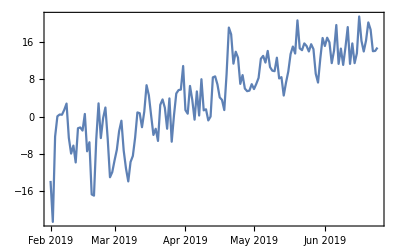

```mathematica
DateListPlot[klebdailytemperaturedata]
```

```mathematica
kleb15minutedata["FirstDate"]
```

```mathematica
TimeSeriesResample[WeatherData["KLEB","Temperature",{{2019,2,1},{2019,12,31},"Hour"}]]
```

```mathematica
TimeSeriesRescale
```

```mathematica
PropertyList[WeatherData]
```

```mathematica
Dataset[WeatherDa
```

```mathematica
dataset=Dataset[{<|"temperature"->2|>,<|"temperature"->3|>}]
Map[Append[#,"newTemperature"->#["temperature"]+2]&,dataset]
```